-Graphics-

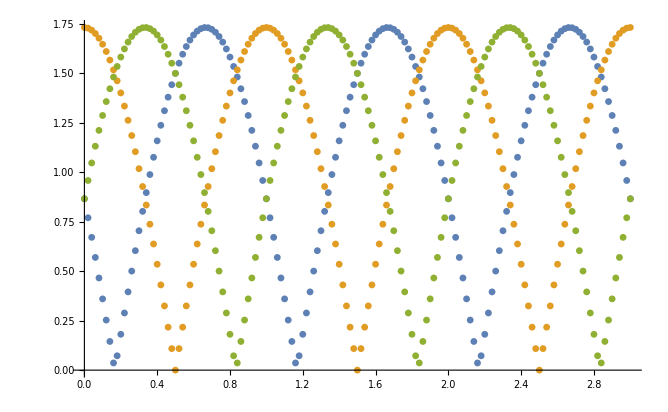

-Graphics-

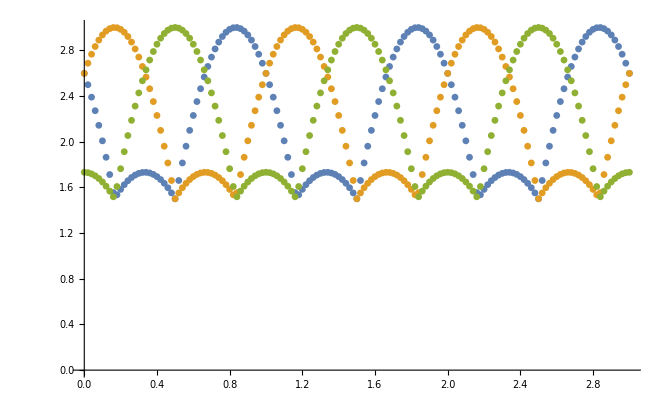

```mathematica
glgl=GridLines->{{
{1/6,Green},{2/6,Green},{3/6,Green},{4/6,Green},{5/6,Green},
{7/6,Green},{8/6,Green},{9/6,Green},{10/6,Green},{11/6,Green},
{1,Red},{2,Red},{3,Red}},None};
YYY[offset_,high_,xx_]:=high*Sin[xx*π+offset*π];
YY1[xx_]=YYY[0,1,xx];
YY2[xx_]=YYY[2/3,1,xx];
YY3[xx_]=YYY[-2/3,1,xx];
ZZ12[xx_]:=Abs[YY1[xx]-YY2[xx]];
ZZ23[xx_]:=Abs[YY2[xx]-YY3[xx]];
ZZ31[xx_]:=Abs[YY3[xx]-YY1[xx]];
ZZ1223[xx_]:=Abs[ZZ12[xx]+ZZ23[xx]];
ZZ2331[xx_]:=Abs[ZZ23[xx]+ZZ31[xx]];
ZZ3112[xx_]:=Abs[ZZ31[xx]+ZZ12[xx]];

SSA1=Table[{x,YY1[x]},{x,0,3,0.02}];
SSA2=Table[{x,YY2[x]},{x,0,3,0.02}];
SSA3=Table[{x,YY3[x]},{x,0,3,0.02}];

SSB1=Table[{x,ZZ12[x]},{x,0,3,0.02}];
SSB2=Table[{x,ZZ23[x]},{x,0,3,0.02}];
SSB3=Table[{x,ZZ31[x]},{x,0,3,0.02}];

SSC1=Table[{x,ZZ1223[x]},{x,0,3,0.02}];
SSC2=Table[{x,ZZ2331[x]},{x,0,3,0.02}];
SSC3=Table[{x,ZZ3112[x]},{x,0,3,0.02}];

SSDAp=Join[Table[{x,ZZ31[x]},{x,0,1/3,0.02}],Table[{x,ZZ12[x]},{x,2/3,3/3,0.02}]];
SSDCp=Join[Table[{x,ZZ23[x]},{x,0,1/3,0.02}],Table[{x,ZZ12[x]},{x,4/3,5/3,0.02}]];

SSDBm=Join[Table[{x,ZZ31[x]},{x,1/3,2/3,0.02}],Table[{x,ZZ23[x]},{x,5/3,6/3,0.02}]];
SSDCm=Join[Table[{x,ZZ12[x]},{x,1/3,2/3,0.02}],Table[{x,ZZ23[x]},{x,3/3,4/3,0.02}]];

SSDBp=Join[Table[{x,ZZ23[x]},{x,2/3,3/3,0.02}],Table[{x,ZZ31[x]},{x,4/3,5/3,0.02}]];
SSDAm=Join[Table[{x,ZZ31[x]},{x,3/3,4/3,0.02}],Table[{x,ZZ12[x]},{x,5/3,6/3,0.02}]];

SSDBmx=Table[{x,0.2},{x,0/3,1/3,0.07}];
SSDApx=Table[{x,0.3},{x,1/3,2/3,0.07}];
SSDCmx=Table[{x,0.2},{x,2/3,3/3,0.07}];
SSDBpx=Table[{x,0.3},{x,3/3,4/3,0.07}];
SSDAmx=Table[{x,0.2},{x,4/3,5/3,0.07}];
SSDCpx=Table[{x,0.3},{x,5/3,6/3,0.07}];

ListPlot[
{SSDAp,SSDCp,SSDBm,SSDCm,SSDBp,SSDAm,
SSDBmx,SSDApx,SSDCmx,SSDBpx,SSDAmx,SSDCpx},glgl,
PlotMarkers->{"A+","C+","B-","C-","B+","A-",
"B-","A+","C-","B+","A-","C+"}]

ListPlot[{SSB1,SSB2,SSB3},glgl]
ListPlot[{SSA1,SSA2,SSA3},glgl,PlotMarkers->{"A","C","B"}]
ListPlot[{SSC1,SSC2,SSC3},glgl]
```